```mathematica
ode=y'[x]+(x+(1+3 x^2)/(1+x+x^3))y[x]-x^3-2x-x^2(1+3 x^2)/(1+x+x^3)==0
```

-2 x-x^3-(x^2 (1+3 x^2))/(1+x+x^3)+(x+(1+3 x^2)/(1+x+x^3)) y[x]+y'[x]==0

```mathematica
generalSolution=FullSimplify[DSolve[ode,y[x],x]]
```

{{y[x]→x^2+(ⅇ^(-x^2/2) C[1])/(1+x+x^3)}}

```mathematica
particularSolution=FullSimplify[DSolve[{ode,y[0]==1},y[x],x]]
```

{{y[x]→x^2+(ⅇ^(-x^2/2))/(1+x+x^3)}}

```mathematica
ya[x_]:=y[x]/.particularSolution[[1]]
```

```mathematica
FullSimplify[D[ya[x],x]]
```

2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)

```mathematica
dyadx[x_]:=2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)
```

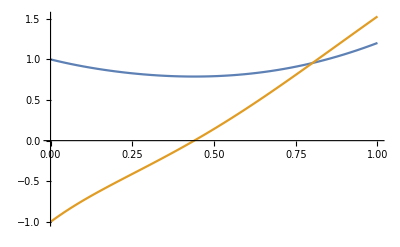

```mathematica
Plot[{ya[x],dyadx[x]},{x,0,1}]
```

```mathematica
Limit[y/(√(1-y^2)),y->1]
```

(-ⅈ) ∞